```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
Clear[extractData];
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/x];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[LinearModelFit[d[[-Min[points,Length[d]];;-1]](*,func*),arg,arg],{d, data}]
```

```mathematica
getScaling[]:=(
fitFunctions={1,x,x^2};
fitPoints=5;

directive={Select[#coupling==J&&#momentum==k&&#interaction==B&]};
keys={"size","gap"};

fits={};
Do[(
Do[(
gap={};
Do[(
AppendTo[gap,extractData[scalingDataset,directive,keys]];
),{B,scalingAvail["interaction"]//Normal}];
AppendTo[fits,<|"coupling"->J,"momentum"->k,"fits"->makeFits[gap,fitFunctions, x,fitPoints]|>];
),{k,scalingAvail["momentum"]//Normal}];
),{J,scalingAvail["coupling"]//Normal}];

Dataset[fits]
)
```

```mathematica
refineScaling[]:=(
scaling = scaling/.x->0;
(*scaling=Table[Table[Table[{beta[[bt]],scaling[[it,jt,bt]]},{bt,Length[beta]}],{jt,Length[scaling[[it]]]}],{it,Length[scaling]}];*)
)
```

```mathematica
getPlot[data_,scaling_,cutoff_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];

plt=ListPlot[data,
PlotRange->{{0,1.0},{0,1.0}},ImageSize->Medium,
Frame->True,Axes->False,Joined->True,
FrameStyle->Directive[Black,20,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 10},
PlotLegends->Placed[Table[StringJoin["L = ",ToString[NumberForm[L,{2,1}]]],{L,Select[qpAvail["size"],#>cutoff&]//Normal}],{0.82,0.78}],
Epilog->Text[
Style[StringJoin["J = ",ToString[NumberForm[J,{2,1}]],"t\n k = ",ToString[NumberForm[k,{2,1}]],"π"],Black,18,FontFamily->"Bookman Old Style"],
{0.2,0.8}],
FrameLabel->{Style["λ",Black,20,FontFamily->"Bookman Old Style"],Style["ΔE",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,12],
PlotStyle->Directive[Dashed],
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}}
];
splt=ListPlot[scaling,
PlotMarkers->{{"×",20},{"×",20}},
PlotStyle->Directive[Black]
];
Show[plt,splt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsGapB[cutoff_,scaling_]:=(

directive={Select[#coupling==J&&#momentum==k&&#size==L&]};
keys={"interaction","gap"};
beta={0.0,1.0};

plots={};
Do[(
Do[(
gap={};
Do[(
data=extractData[qpDataset,directive,keys,False];
If[Length[data]>0&&L>cutoff,AppendTo[gap,data]];
),{L,qpAvail["size"]//Normal}];
scdata=Table[Flatten[{beta[[bt]],Normal[scaling[Select[#coupling==J&&#momentum==k&],"fits"]][[1,bt]][{"BestFit"}]/.x->0}],{bt,Length[beta]}];
AppendTo[plots,getPlot[gap,scdata,cutoff]];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"12-2-28_0.0-1.0-1.0"};
scaling ={};
Do[(
scalingDataset=Dataset[getAssoc["qp",JRange,tail]];
scalingAvail=Dataset[getStruct[scalingDataset]];
AppendTo[scaling,getScaling[]];
),{tail,tails}]

ScalingInfo={{"coupling","momentum","interaction","fit","errors"}};
BRange={0.0,1.0};
Do[(
linfit=Normal[Select[scaling[[1]],#coupling==ToExpression[J]&&#momentum==k&][Take,"fits"]][[1,it]];
AppendTo[ScalingInfo,{J,k,BRange[[it]],linfit[{"BestFit"}][[1]],linfit[{"ParameterTable"}][[1]]}];
),{J,JRange},{k,{0.0,0.5,1.0}},{it,Length[BRange]}];

tails={"12-4-28_0.0-0.1-1.0"};
BPlots={};
Do[(
cutoff=16;
qpDataset=Dataset[getAssoc["qp",JRange,tails[[it]]]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["ΔE: J ∈ ",ToString[JRange]," @ ", tails[[it]]],16]];
AppendTo[BPlots,makePlotsGapB[cutoff,scaling[[it]]]];
),{it,Length[tails]}]
```

ΔE: J ∈ {0.4} @ 12-4-28_0.0-0.1-1.0

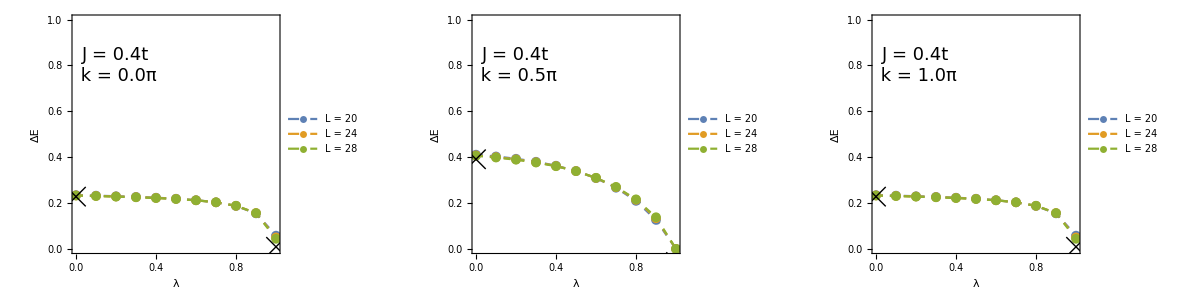

```mathematica
Do[(
kDim=Length[DeleteDuplicates[scaling[[it]][Take,"momentum"]]];
plots=ArrayReshape[BPlots[[it]],{Length[BPlots[[it]]]/kDim,kDim}];
Print[Grid[plots]];
),{it,Length[BPlots]}]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/gap/",
"gapB_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,BPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)
```

```mathematica
SavePlots[]
```

```mathematica
errTab=Grid[ScalingInfo,Frame->All,Background->{{{{None,None,None,LightGreen,LightYellow}},{0->Black}},{{{LightRed,LightBlue}},{1->LightGray}}}]
```

coupling | momentum | interaction | fit | errors
0.4 | 0. | 0. | 0.227927+0.148704 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.227927 | 0.00470741 | 48.4188 | 0.0000193982
x | 0.148704 | 0.110605 | 1.34446 | 0.271419
0.4 | 0. | 1. | 0.00914137+0.983055 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00914137 | 0.00171301 | 5.33644 | 0.0128637
x | 0.983055 | 0.0402487 | 24.4245 | 0.000150445
0.4 | 0.5 | 0. | 0.390993+0.405858 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.390993 | 0.000718067 | 544.507 | 1.36601×10^-8
x | 0.405858 | 0.0125524 | 32.333 | 0.0000650188
0.4 | 0.5 | 1. | -0.0571287+5.61957 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0571287 | 0.00817588 | -6.98747 | 0.00601703
x | 5.61957 | 0.142921 | 39.3193 | 0.0000361944
0.4 | 1. | 0. | 0.227927+0.148704 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.227927 | 0.00470741 | 48.4188 | 0.0000193982
x | 0.148704 | 0.110605 | 1.34446 | 0.271419
0.4 | 1. | 1. | 0.00914137+0.983055 x |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00914137 | 0.00171301 | 5.33644 | 0.0128637
x | 0.983055 | 0.0402487 | 24.4245 | 0.000150445

```mathematica
(*Export["fits_errTab.pdf",errTab]*)
```